```mathematica
AbsoluteTiming[Get[FileNameJoin[{NotebookDirectory[],"FunctionDefinitions.wl"}]]]
ClearAll[SyncDownValues];
SetAttributes[SyncDownValues,HoldAll];
SyncDownValues[M_Symbol]:=(DownValues[M]={DownValues[M],ParallelEvaluate[DownValues[M],DistributedContexts->None]}//Association//Normal;);
```

{23.212,Null}

## Constructing a cache of results

### SDP Results

```mathematica
ClearAll[CachedSDPResult];
SetAttributes[CachedSDPResult,HoldAll];
CachedSDPResult[rhoIn_,rhoFin_,t_?(VectorQ[#,NumericQ]&),HoldPattern[Hamiltonian[ω_,Δω_,DiagonalMatrix[{XX_?NumericQ,YY_?NumericQ,ZZ_}]]]]:=
CachedSDPResult[rhoIn,rhoFin,t,Hamiltonian[ω,Δω,DiagonalMatrix[{XX,YY,ZZ}]]]=SDPResult[rhoIn,rhoFin,Evaluate[N[t]],Hamiltonian[ω,Δω,DiagonalMatrix[{XX,YY,ZZ}]]];
```

#### Detuned initial state |0><0|

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5/Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedSDPResult];
]
```

#### Detuned initial state |+><+|

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedSDPResult];
]
```

#### Detuned initial state |+><+| against ZZ coupling

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω
},
{fun={γ,z}|->SDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Evaluate[N[Δω]],DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]["Population"]},
KeyValueMap[
With[{γ=#1[[1]],z=#1[[2]],res=#2},
CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]=<|"Population"->res|>
]&,ParallelDensityPlotData[fun,{γ,0,1},{z,0,1},"MaxIters"->4]];
]
```

#### Detuned initial state 0.9 |0><0| + 0.1 |1><1| (rhoQubit[{0,0,4/5}])

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,4/5}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedSDPResult];
]
```

### Optimizing over unitaries

```mathematica
SetAttributes[CachedUnitaryStrategy,HoldAll];
CachedUnitaryStrategy[rhoIn_,rhoFin_,t_,HoldPattern[Hamiltonian[ω_,Δω_,DiagonalMatrix[{XX_?NumericQ,YY_?NumericQ,ZZ_}]]]]:=CachedUnitaryStrategy[rhoIn,rhoFin,t,Hamiltonian[ω,Δω,DiagonalMatrix[{XX,YY,ZZ}]]]=UnitaryStrategy[rhoIn,rhoFin,Evaluate[N[t]],Hamiltonian[ω,Δω,DiagonalMatrix[{XX,YY,ZZ}]]];
```

#### Detuned initial state |0><0|

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedUnitaryStrategy];
]
```

#### Detuned initial state |+><+|

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedUnitaryStrategy];
]
```

#### Detuned initial state |+><+| against ZZ coupling

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω
},
{fun={γ,z}|->UnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Evaluate[N[Δω]],DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]["Population"]},
KeyValueMap[
With[{γ=#1[[1]],z=#1[[2]],res=#2},
CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]=<|"Population"->res|>
]&,ParallelDensityPlotData[fun,{γ,0,1},{z,0,1},"MaxIters"->4]];
]
```

#### Detuned initial state 0.9 |0><0| + 0.1 |1><1| (rhoQubit[{0,0,4/5}])

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,4/5}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange=Range@@{0,1,10^-3}
},
{fun=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]},
ParallelMap[fun,plottingRange];
SyncDownValues[CachedUnitaryStrategy];
]
```

## Plots

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"..",".."}]]
```

/Users

```mathematica
Needs["MaTeX`"]
MaTeX["x^2"]
```

-Graphics-

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,bm}"},FontSize->14]
MaTeX["\\matrixel{1}{a^\\dag}{0}_\\beta=1"]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{physics,bm}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→14,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

-Graphics-

```mathematica
StyledPlot[data_]:=ListLinePlot[
data,
PlotTheme->{"Academic","DashedLines"},
PlotRange->{.45,1.05},
PlotMarkers->None,
PlotStyle->{{AbsoluteThickness[2],Opacity[1]},{AbsoluteThickness[3],Opacity[.6]}},
FrameLabel->{ MaTeX["g_\\perp"],MaTeX["\\matrixel{0}{\\rho_{out}}{0}"]},
GridLines->Automatic,
GridLinesStyle->LightGray,
ImageSize->320
];
```

### fig:OptimalVsUnitaryZeroState

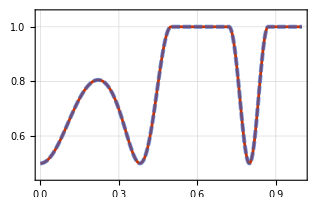

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,1}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω,
plottingRange={γ,0,1,10^-3}
},
{
fun1=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]],
fun2=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]
},
StyledPlot[{
Table[{γ,fun1[γ]["Population"]},plottingRange],Table[{γ,fun2[γ]["Population"]},plottingRange]
}]
]
```

```mathematica
Export["Figures/Plots/OptimalVsUnitaryZeroState.png",,ImageResolution->600]
```

Figures/Plots/OptimalVsUnitaryZeroState.png

### fig:OptimalVsUnitaryPlusState

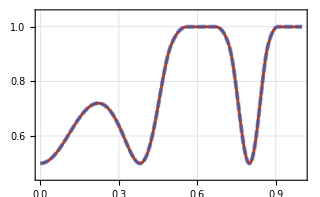

```mathematica
With[
{
ω=1000,
Δω=1,
rhoFin=rhoQubit[{0,0,1}],
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}]
},
{
t=5Δω,
plottingRange={γ,0,1,10^-3}
},
{fun1=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]],
fun2=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]
},
StyledPlot[{
Table[{γ,fun1[γ]["Population"]},plottingRange],Table[{γ,fun2[γ]["Population"]},plottingRange]
}]
]
```

```mathematica
Export["Figures/Plots/OptimalVsUnitaryPlusState.png",]
```

Figures/Plots/OptimalVsUnitaryPlusState.png

#### Detuned initial state |+><+| against ZZ coupling

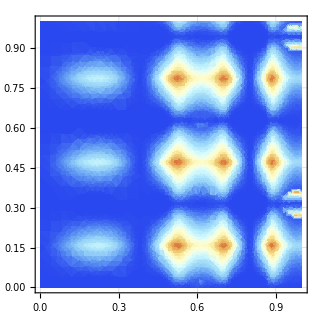

```mathematica
With[
{
ω=1000,
Δω=1,
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{1,0,0}],
rhoFin=rhoQubit[{0,0,1}]
},
{
t=5Δω
},
{
contours=Range[0,1,.05]
},
{
fun1={γ,z}|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]["Population"],
fun2={γ,z}|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,z Δω}]]]["Population"]
},
ParallelDensityPlotData[Abs[fun2[##]-fun1[##]]&,{γ,0,1},{z,0,1},"MaxIters"->4]//ListDensityPlot[#,
PlotRangePadding->None,
Mesh->{contours},MeshFunctions->{#3&},
PlotRange->{0,0.3},
ColorFunction->"LightTemperatureMap",
ClippingStyle->{Yellow,Green},
GridLines->Automatic,
GridLinesStyle->Directive[AbsoluteThickness[Tiny],Black],
PlotLegends->Placed[Row[{Spacer[30],BarLegend[{"LightTemperatureMap",{0,0.3}},
LegendLayout->"Row",
LabelStyle->Directive[Black,FontFamily->"STIX Two Text",FontSize->12],
Method->{TicksStyle->Directive[Black]},
LegendLabel->MaTeX["\\;\\;\\matrixel{0}{\\rho^{\\text{SDP}}_{out}-\\rho_{out}}{0}"]
]}],Top],
FrameLabel->{ MaTeX["g_\\perp"],MaTeX["g_\\parallel"]},
ImageSize->320
]&
]
```

```mathematica
Export["Figures/Plots/OptimalVsUnitaryPlusState.png",,ImageResolution->600]
```

Figures/Plots/OptimalVsUnitaryPlusState.png

```mathematica
{a,b}*{c,d}
```

{a c,b d}

### fig:OptimalVsUnitaryMixed

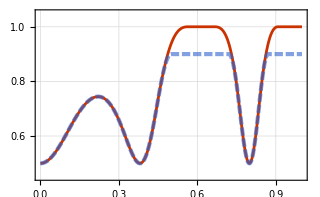

```mathematica
With[
{
ω=1000,
Δω=1,
rhoFin=rhoQubit[{0,0,1}],
rhoIn=rhoQubit[{0,0,0}]⊗rhoQubit[{0,0,4/5}]
},
{
t=5Δω,
plottingRange={γ,0,1,10^-3}
},
{fun1=γ|->CachedSDPResult[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]],
fun2=γ|->CachedUnitaryStrategy[rhoIn,rhoFin,{t,t,t},Hamiltonian[ω,Δω,DiagonalMatrix[{γ Δω,γ Δω,0}]]]
},
StyledPlot[{
Table[{γ,fun1[γ]["Population"]},plottingRange],Table[{γ,fun2[γ]["Population"]},plottingRange]
}]
]
```

```mathematica
Export["Figures/Plots/OptimalVsUnitaryMixed.png",,ImageResolution->600]
```

Figures/Plots/OptimalVsUnitaryMixed.png